```mathematica
(***Part 1***)
(**Density Functions**)

ClearAll[x,y,z,r,θ,ϕ,ρ];

NoseDensity[x_,y_,z_]=x^2+y/(.05)+z^2;
RecoveryDensity[x_,y_,z_]=(((2 x)(2x))+y+z^4);
(*Had to do this because of mathmatic error coding due to function e redefinitions*)Clear[EngineDensity,x,y,z]
EngineDensity[x_,y_,z_]=18 ⅇ^x+15y+35z;
```

```mathematica
(**Mass Functions and Outputs**)

(*Nose Mass*)
x=r Cos[θ];
y=r Sin[θ];
z=z;

MassNose=∫_0^(5√5) ∫_0^(2π) ∫_0^(20-4/25 r^2) (NoseDensity[x,y,z])rⅆzⅆθⅆr

(*Recovery Mass*)
x=ρ Sin[ϕ] Cos[θ];
y=ρ Sin[ϕ] Sin[θ];
z=ρ Cos[ϕ];
MassRecovery=∫_0^9 ∫_0^π ∫_0^(2π) (RecoveryDensity[x,y,z])*ρ^2  Sin[ϕ]ⅆθⅆϕⅆρ;
N[MassRecovery]

(*Engine Mass*)

ClearAll[x,y,z];
MassEngine=∫_0^15 ∫_0^19 ∫_0^50 EngineDensity[x,y,z]ⅆzⅆyⅆx;
N[MassEngine]

(*Body Mass*)

MassBody=1200000

(*Fins Mass*)

MassFins=500500

N[MassRocket=MassBody+MassEngine+MassRecovery+MassFins+MassNose];

Gravity=32.2;

WeightRocket=MassRocket*Gravity
```

343612.

1.91515×10^6

5.59147×10^10

1200000

500500

1.80058×10^12

```mathematica
(**Center of Masses**)

(*Center of Mass Nose*)
x=r Cos[θ];
y=r Sin[θ];
z=z;
(*adding the new defintions of x y and z are critical for making this function work*)
xbarnoseo=1/MassNose ∫_0^(5√5) ∫_0^(2π) ∫_0^(20-4/25 r^2) x*NoseDensity[x,y,z]*rⅆzⅆθⅆr;
ybarnoseo=1/MassNose ∫_0^(5√5) ∫_0^(2π) ∫_0^(20-4/25 r^2) y*NoseDensity[x,y,z]*rⅆzⅆθⅆr;
zbarnoseo=1/MassNose ∫_0^(5√5) ∫_0^(2π) ∫_0^(20-4/25 r^2) z*NoseDensity[x,y,z]*rⅆzⅆθⅆr;
centermassnose={xbarnoseo,ybarnoseo,zbarnoseo}+{15,10,235}

(*Center of Mass Recovery*)
x=ρ Sin[ϕ] Cos[θ];
y=ρ Sin[ϕ] Sin[θ];
z=ρ Cos[ϕ];

xbarrecoveryo=1/MassRecovery∫_0^9 ∫_0^π ∫_0^(2π) x(RecoveryDensity[x,y,z])ρ^2 Sin[ϕ]ⅆθⅆϕⅆρ;
ybarrecoveryo=1/MassRecovery∫_0^9 ∫_0^π ∫_0^(2π) y(RecoveryDensity[x,y,z])ρ^2 Sin[ϕ]ⅆθⅆϕⅆρ;
zbarrecoveryo=1/MassRecovery∫_0^9 ∫_0^π ∫_0^(2π) z(RecoveryDensity[x,y,z])ρ^2 Sin[ϕ]ⅆθⅆϕⅆρ;
N[centermassrecovery={xbarrecoveryo,ybarrecoveryo,zbarrecoveryo}+{18,13,190}]

(*Center of Mass Engine*)
ClearAll[x,y,z];

xbarengineo=1/MassEngine∫_0^15 ∫_0^19 ∫_0^50 x EngineDensity[x,y,z]ⅆzⅆyⅆx;
ybarengineo=1/MassEngine∫_0^15 ∫_0^19 ∫_0^50 y EngineDensity[x,y,z]ⅆzⅆyⅆx;
zbarengineo=1/MassEngine∫_0^15 ∫_0^19 ∫_0^50 z EngineDensity[x,y,z]ⅆzⅆyⅆx;
centermassengine={xbarengineo,ybarengineo,zbarengineo}+{5,12,70};
N[centermassengine]

(*Center of Mass Body*)

xbarbodyo=1.8;
ybarbodyo=3.0;
zbarbodyo=2.5;

centermassbody={xbarbodyo,ybarbodyo,zbarbodyo}+{8,10,130}

(*Center of Mass Fins*)

xbarfinso=1.0;
ybarfinso=1.0;
zbarfinso=2.7;

centermassfins={xbarfinso,ybarfinso,zbarfinso}+{10,14,25}
```

{15.,14.7619,245.333}

{18.,13.0258,190.}

{18.9983,21.5001,95.0019}

{9.8,13.,132.5}

{11.,15.,27.7}

```mathematica
(**New Moments**)

(*New Moment of the Nose*)
N[NewMomentNose=MassNose*centermassnose]

(*New Moment of the Recovery*)
N[NewMomentRecovery=MassRecovery*centermassrecovery]

(*New Moment of the Body*)
N[NewMomentBody=MassBody*centermassbody]

(*New Moment of the Engine*)
N[NewMomentEngine=MassEngine*centermassengine]

(*New Moment of the Fins*)
N[NewMomentFins=MassFins*centermassfins]
```

{5.15418×10^6,5.07236×10^6,8.42994×10^7}

{3.44727×10^7,2.49464×10^7,3.63878×10^8}

{1.176×10^7,1.56×10^7,1.59×10^8}

{1.06228×10^12,1.20217×10^12,5.312×10^12}

{5.5055×10^6,7.5075×10^6,1.38639×10^7}

```mathematica
(**Center of Mass of the Rocket**)
centermassrocket=(NewMomentNose+NewMomentBody+NewMomentEngine+NewMomentFins+NewMomentRecovery)/MassRocket
```

{18.998,21.4995,95.0062}

```mathematica
(***Part 2***)
(*1. Check to see your group has created a valid Joint Density Function*)
Subscript[μ, y]=10.56;
Subscript[σ, y]=1.03;
Subscript[μ, x]=6.18;
Subscript[σ, x]=.98;

f1[x_]=1/(Subscript[σ, x] √(2π))ⅇ^(-1/2((x-Subscript[μ, x])/Subscript[σ, x])^2);
f2[y_]=1/(Subscript[σ, y] √(2π))ⅇ^(-1/2((y-Subscript[μ, y])/Subscript[σ, y])^2);
f[x_,y_]= f1[x]*f2[y]
```

0.157673 ⅇ^(-0.520616 (-6.18+x)^2-0.471298 (-10.56+y)^2)

```mathematica
(*2.  Create a 3D (surface) plot of the Joint Density Function of the time (months) for the boosters and payload fairing. Label your axes and give your graph a title*)
Plot3D[f[x,y],{x, 0, 12}, {y, 0, 12} , PlotLabel->"Rocket Failure", AxesLabel->{Pair of Booster Months, Faring  Months,z}, PlotLegends->{"f(x,y)"},Axes->True]
```

-Graphics3D-

```mathematica
(*3. What is the probability that a pair of boosters and a payload fairing both last at least 8 months*)
```

```mathematica
∫_8^∞ ∫_8^∞ f[x,y]ⅆyⅆx
```

```mathematica
0.03144068209972941-5.24592432035211*^-15 ⅈ
The number above represents the percentage that both the payload fairing and the pair of boosters failing in 8 month;
```

```mathematica
(*4. What is the probability that a pair of boosters and a payload fairing both fail between 5 and 15
months*)
∫_5^15 ∫_5^15 f[x,y]ⅆyⅆx
```

0.0489535

```mathematica
The number above represents the success percentage that both the payload fairing and the pair of boosters failing between 5 and 15 months.
```

```mathematica
(*5. Do you recommend the maintenance team be ready to replace just the boosters, just a payload fairing,or both the boosters and payload fairing by the 10th month? Why or why not*)
```

```mathematica
The group recommends replacing both the fairing and the boosters because the fairing is almost at the end of its life at 10.56 months on average. The boosters have also reached past their average life of 6.18 months so their is bound to be issues. There is also an 88% chance that both will fail between 5 and 15 months;

(***Part 3***)
```

```mathematica
(*The values of K and L that maximize output if the total input costs (K + L) are fixed at $98000*)
c = 98000;
f[K_ , L_] = 0.00005 K^0.40 L^0.60;
g[K_ , L_] = K+L;
Solve[{D[f[K,L], K]==λ*D[g[K,L], K], D[f[K,L], L]==λ*D[g[K,L], L], g[K,L] ==c}, {K,L,λ}]
```

{{K→39200.,L→58800.,λ→0.0000255085}}

```mathematica
(*Number of boosters that can be made with a $98,000 constraint.*)
0.00005*(39200)^0.40*(58800)^0.60
```

2.49983

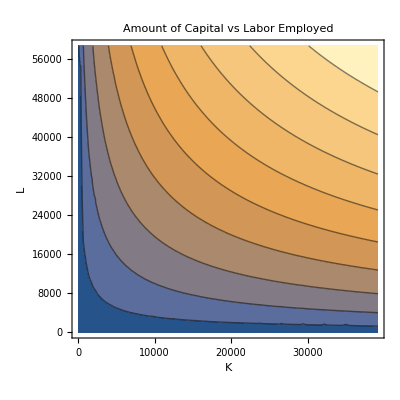

```mathematica
(*Create a contour plot of the objective function and the constraint in part 1.*)
ContourPlot[0.00005 K^0.40 L^0.60,{K,0,39200},{L,0,58800},PlotLabel->"Amount of Capital vs Labor Employed", AxesLabel->Automatic]
```

```mathematica
clear[c,K,L]
```

clear[98000,K,L]

```mathematica
(*Find the new maximum output if the input costs are increased to $158,000.*)
c = 158000;
f[K_ , L_] = 0.00005 K^0.40 L^0.60;
g[K_ , L_] = K+L;
Solve[{D[f[K,L], K]==λ*D[g[K,L], K], D[f[K,L], L]==λ*D[g[K,L], L], g[K,L] ==c}, {K,L,λ}]
```

{{K→63200.,L→94800.,λ→0.0000255085}}

```mathematica
(*Number of boosters that can be made with a $158,000 constraint*)
```

```mathematica
0.00005*(63200)^0.40*(94800)^0.60
```

4.03034